```mathematica
(*The purpose of this code is to solve for the 1D domain wall for Superconductivity. The calculations in this code are as follows. 
Section 1 - Solving the ODE numetically.
Here we just solve the G-L ODE numnerically. The domain has been approximated as [-L,L] so that we can take limits. The ODE is taken from ST. James and Sarma p 38/288.
We have also tried solving for f(x) if we assume h(x).
Section 2 - Here we try to solve the problem Variationally.  We use two choices of test functions
Choice 1 --> tanh for u and h
Choice 2 --> Only varies in a window [-l,l]  where it continuously interpolates between the bulk SC and bulk normal values.
*)
```

```mathematica
ClearAll["Global`*"]
```

## (*Solving the ODE numericaly*)

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
Needs["NDSolve`FEM`"]
```

```mathematica
κ=5;
eqn1 = -1/κ^2*f''[x]+A[x]^2*f[x]-f[x]+f[x]^3
eqn2 = A''[x]+A[x]*f[x]^2
NDSolve[{-1/κ^2*f''[x]+A[x]^2*f[x]-f[x]+f[x]^3==0,A''[x]+A[x]*f[x]^2==0,f[-1]==0,A'[-1]==1/Sqrt[2],f[1]==1,A[1]==0},{f[x],A[x]},{x,-1,1},MaxSteps->10000,PrecisionGoal->18,AccuracyGoal->18,WorkingPrecision->30,Method->"StiffnessSwitching"]
```

-f[x]+A[x]^2 f[x]+f[x]^3-f''[x]/25

A[x] f[x]^2+A''[x]

NDSolve::ndsz: At x == -0.693718720657495918460383354196, step size is effectively zero; singularity or stiff system suspected.

NDSolve[{-f[x]+A[x]^2 f[x]+f[x]^3-f''[x]/25==0,A[x] f[x]^2+A''[x]==0,f[-1]==0,A'[-1]==1/(√2),f[1]==1,A[1]==0},{f[x],A[x]},{x,-1,1},MaxSteps→10000,PrecisionGoal→18,AccuracyGoal→18,WorkingPrecision→30,Method→StiffnessSwitching]

```mathematica
(*NDSolve[{-1/κ^2*f''[x]+1/f[x]^3(h'[x])^2==f[x]^1-f[x]^3,f[x]^2*h[x]+2/f[x]*f'[x]*h'[x]+1*h''[x]==0,f[-L]==sml,h[-L]==1/Sqrt[2],f[L]==1,h[L]==sml},{f[x],h[x]},{x,-L,L}]*)
```

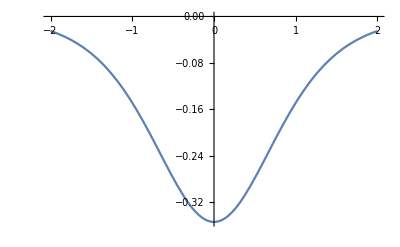

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == -8368.64551252846152783401892904.

{{f[x]→InterpolatingFunction[{{-10000.0000000000000000000000000, -8368.64551252846152783401892904}}, <>][x]}}

-Graphics-

```mathematica
h0[x_,a_]:=1/(2*Sqrt[2])*(Tanh[-x/a]-1)+1/Sqrt[2]
a0=1;
hp[x_]:=-Sech[x]^2/(2 √2)
Plot[hp[x],{x,-2,2}]
(*f[x]^3*h0[x,a0]+2f'[x]*D[h0[x,a0],x]+f[x]*D[h0[x,a0],{x,2}]==0
D[h0[x,a0],x]
s=NDSolve[{-1/κ^2*f''[x]+1/f[x]^3(-Sech[x]^2/(2 √2))^2==f[x]^1-f[x]^3,f[-L]==sml,f'[-L]==sml},{f[x]},{x,-L,L},Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->20]
Plot[Evaluate[f[x]/.s],{x,-L,L},PlotRange->All]*)
sol=NDSolve[{-f[x]^3/κ^2*f''[x]+(hp[x])^2==f[x]^4-f[x]^6,f[-L]==10^-4,f'[-L]==10^-6},{f[x]},{x,-L,L},MaxSteps->10000,PrecisionGoal->18,AccuracyGoal->18,WorkingPrecision->30,Method->"StiffnessSwitching"]
Plot[Evaluate[f[x]/. sol],{x,-L,L},PlotRange->All]
```

```mathematica
(*sol2=NDSolve[{-1/κ^2*u''[x]==u[x]^1-u[x]^3,u[1]==.5,u[L]==1},{u[x]},{x,1,L},MaxSteps->1000000,PrecisionGoal->18,AccuracyGoal->18,Method->"StiffnessSwitching"]
Plot[Evaluate[u[x]/. sol2],{x,1,L},PlotRange->All]*)
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InitializePDECoefficients::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

FindRoot::jsing1: Encountered a singular Jacobian at the point {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«72»}. Try perturbing the initial point(s).

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

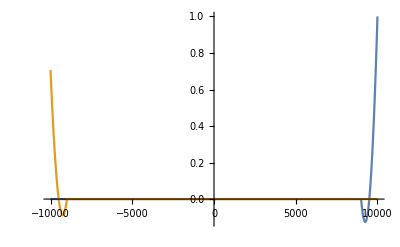

```mathematica
ic1=DirichletCondition[f[x]==0+sml,x==-L];
ic2=DirichletCondition[f[x]==1-sml,x==L];
ic3=DirichletCondition[h[x]==1/Sqrt[2]+sml,x==-L];
ic4=DirichletCondition[h[x]==sml,x==L];
ode1=-f[x]^3/κ^2*f''[x]+(h'[x])^2==f[x]^4-f[x]^6;
ode2=f[x]^3*h[x]+2f'[x]*h'[x]+f[x]*h''[x]==0;
sol3=NDSolve[{ode1,ode2,ic1,ic2,ic3,ic4},{f,h},{x,-L,L},Method->{"FiniteElement"}];
Plot[{Evaluate[f[x]/.sol3],Evaluate[h[x]/.sol3]},{x,-L,L},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
ic41={u[-L]==0+sml,u[L]==1-sml,A'[-L]==1/Sqrt[2],A[L]==1};
ode21=-1/κ^2*u''[x]+A[x]^2*u[x]==u[x]^1-u[x]^3;
ode22=u[x]^2*A[x]+A''[x]==0;
sol4=NDSolve[{ode21,ode22,ic41},{u,A},{x,-L,L},Method->{"FiniteElement"}];
Plot[{Evaluate[u[x]/.sol3],Evaluate[A[x]/.sol3]},{x,-L,L},AxesOrigin->{0,0},PlotRange->All]
```

NDSolve::fembderiv: The expression A'[-10000]==1/(√2) given as a spatial boundary condition for the possibly automatically chosen finite element method should not have explicit derivatives of the dependent variables. NeumannValue should be used to specify spatial derivatives at the boundary.

-Graphics-